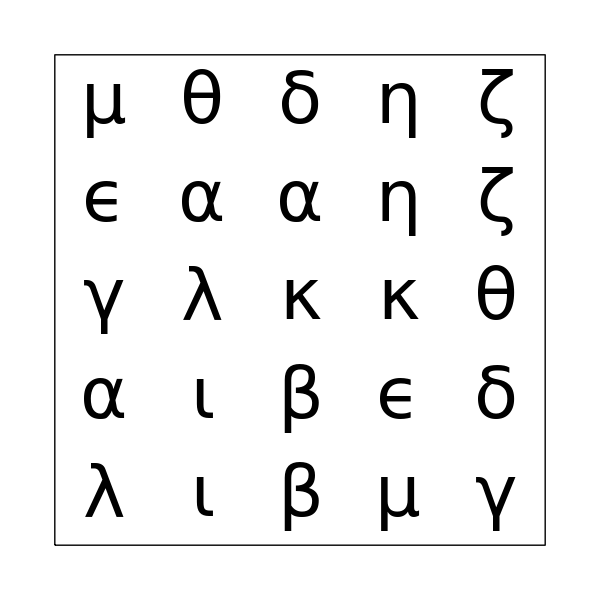

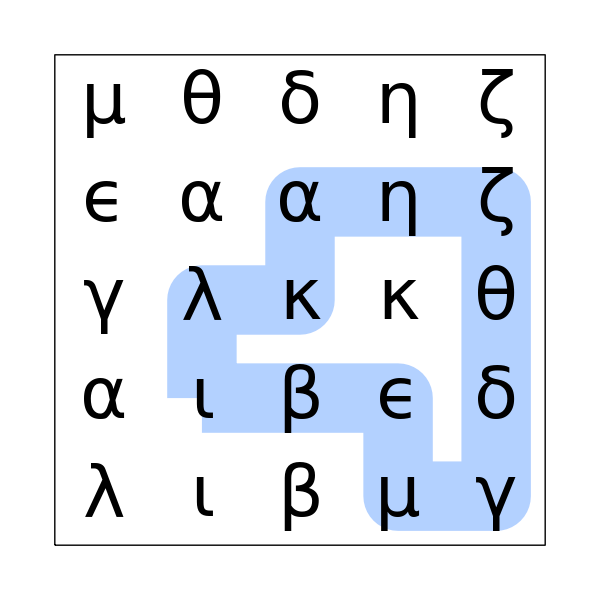

```mathematica
width=4;
paths={};
stack=Select[Take[Flatten[Table[{{i,j},{i+1,j}},{i,1,width},{j,1,width}],1],Floor[width^2/2]+1],#[[1,2]]<width&];
While[Length[stack]>0,
cur=First[stack];
stack=Rest[stack];
If[Length[cur]==Floor[width^2/2]+1&&First[cur]==Last[cur],AppendTo[paths,cur]];
pos=Last[cur];
next=Select[Complement[Map[pos+#&,{{0,1},{1,0},{0,-1},{-1,0}}],Rest[cur]],1≤#[[1]]≤width&&1≤#[[2]]≤width&& Sort[{First[cur],#}]=={First[cur],#}&];
stack=Map[Append[cur,#]&,next]~Join~stack;
];paths=Map[Drop[#,-1]&,paths];
```

```mathematica
Length[paths4x4]
```

26

```mathematica
Length[paths5x5]
```

445

```mathematica
Length[paths6x6]
```

32172

```mathematica
choose:=Module[{},
w=Floor[width^2/2];
A=Table[1,{width},{width}];
For[i=2,i≤w,i++,
r1=RandomInteger[{1,width}];r2=RandomInteger[{1,width}];
While[A[[r1,r2]]>1,
r1=RandomInteger[{1,width}];r2=RandomInteger[{1,width}]];
A[[r1,r2]]=i;
r1=RandomInteger[{1,width}];r2=RandomInteger[{1,width}];
While[A[[r1,r2]]>1,
r1=RandomInteger[{1,width}];r2=RandomInteger[{1,width}]];
A[[r1,r2]]=i];A]
```

```mathematica
beforepic[A_]:=Graphics[{Line[{{0,0},{0,width},{width,width},{width,0},{0,0}}],MapIndexed[Text[Style[#1,FontSize->16],#2-1/2]&,A,{2}]},ImageSize->25width]
```

```mathematica
afterpic[A_,p_]:=Graphics[{Hue[.6,.3],AbsoluteThickness[16],Line[(p~Join~{First[p]})-1/2],Black,AbsoluteThickness[1],Line[{{0,0},{0,width},{width,width},{width,0},{0,0}}],MapIndexed[Text[Style[#1,FontSize->16],#2-1/2]&,A,{2}]},ImageSize->25width]
```

-Graphics-

```mathematica
For[k=1,k<200,k++
choose;
p=Select[paths,Sort[Extract[A,#]]==Range[width^2/2]&];
If[Length[p]==1,Print[beforepic[A]];Print[afterpic[A,p[[1]]]]]]
```

## 4x4

-Graphics-

-Graphics-

-Graphics-

«77 more identical outputs»

## 5x5

-Graphics-

-Graphics-

-Graphics-

«215 more identical outputs»

## 6x6

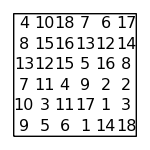

-Graphics-

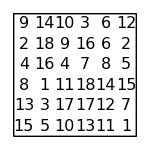

-Graphics-

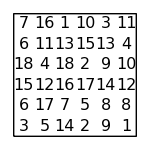

-Graphics-

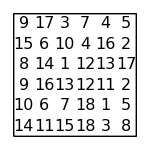

-Graphics-

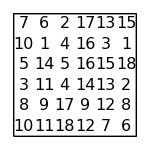

-Graphics-

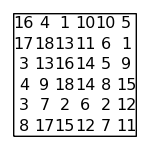

-Graphics-

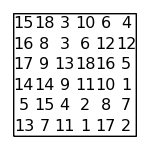

-Graphics-

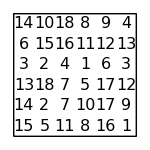

-Graphics-

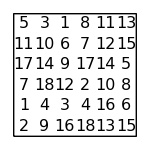

-Graphics-

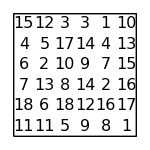

-Graphics-

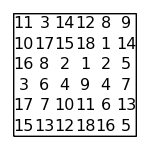

-Graphics-

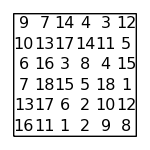

-Graphics-

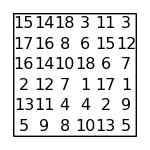

-Graphics-

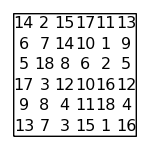

-Graphics-

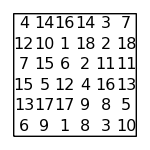

-Graphics-

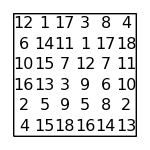

-Graphics-

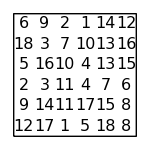

-Graphics-

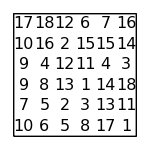

-Graphics-

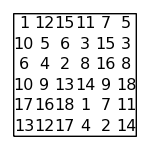

-Graphics-

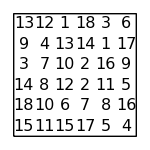

-Graphics-

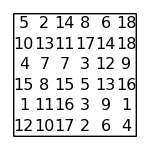

-Graphics-

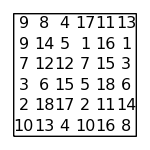

-Graphics-

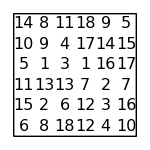

-Graphics-

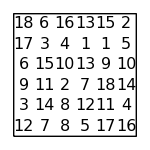

-Graphics-

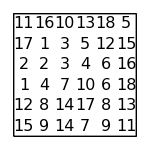

-Graphics-

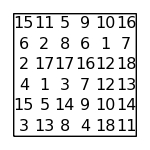

-Graphics-

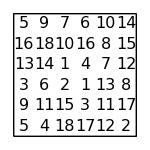

-Graphics-

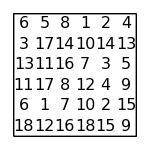

-Graphics-

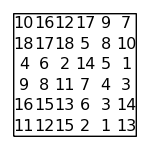

-Graphics-

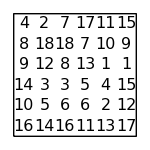

-Graphics-

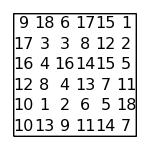

-Graphics-

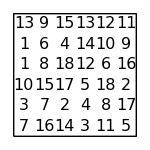

-Graphics-

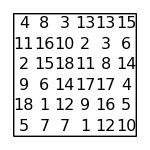

-Graphics-

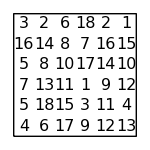

-Graphics-

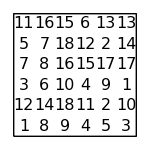

-Graphics-

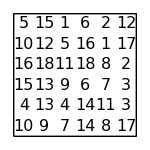

-Graphics-

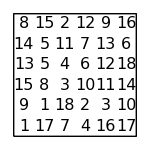

-Graphics-

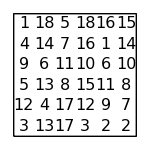

-Graphics-

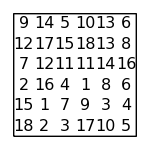

-Graphics-

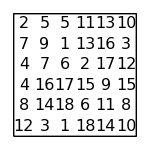

-Graphics-

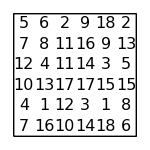

-Graphics-

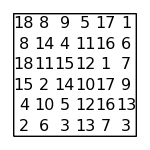

-Graphics-

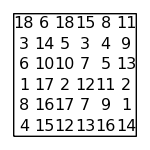

-Graphics-

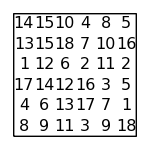

-Graphics-

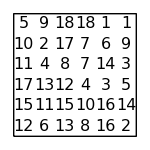

-Graphics-

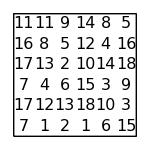

-Graphics-

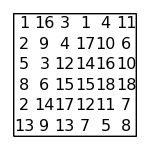

-Graphics-

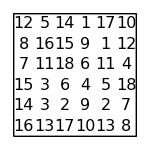

-Graphics-

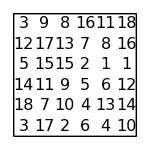

-Graphics-

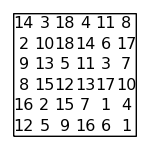

-Graphics-

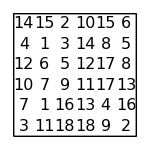

-Graphics-

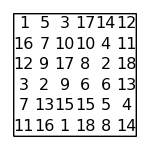

-Graphics-

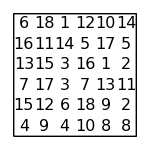

-Graphics-

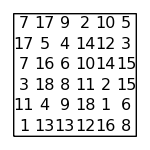

-Graphics-

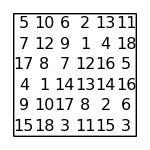

-Graphics-

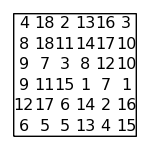

-Graphics-

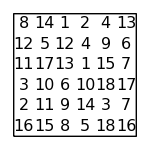

-Graphics-

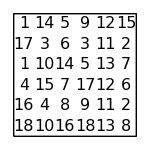

-Graphics-

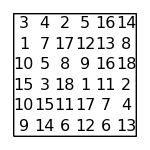

-Graphics-

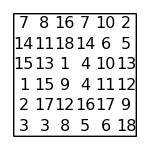

-Graphics-

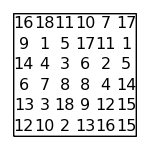

-Graphics-

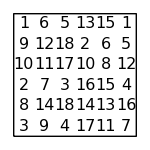

-Graphics-

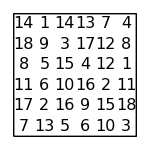

-Graphics-

-Graphics-

-Graphics-

-Graphics-

«81 more identical outputs»